2.

Scalar ω^2 = {0.0251737,0.100697,0.226585,0.402884,0.629705,0.90727}

✅  Scalar sector stable

Vector ω^2 = {0.025171,0.100685,0.226557,0.402844,0.629679,0.907308}

Tensor ω^2 = {0.0251787,0.100716,0.226617,0.402915,0.6297,0.90718}

✅  Vector sector stable

✅  Tensor sector stable

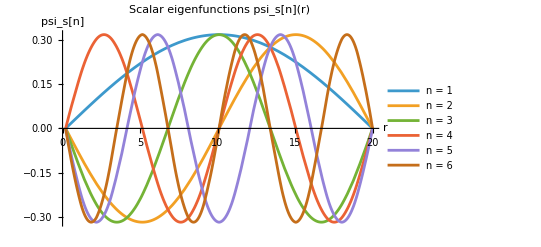

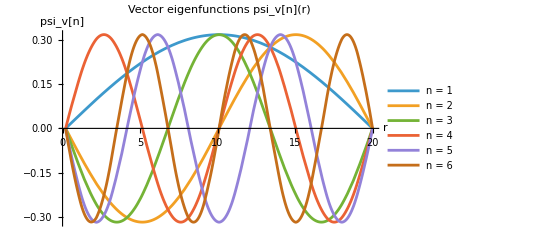

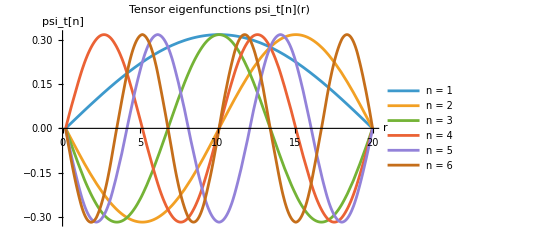

```mathematica
(***********************************************************)(*2. Scalar/Vector/Tensor sectors via NDEigensystem*)(***********************************************************)(*---Geometry& potential parameters (1 mm wormhole)---*)ClearAll["Global`*"];

(*Physical scale:take r in meters,with R0=1 mm*)
A=0.01;                    (*potential strength*)
R0=2.0             (*2m throat radius*)
w=0.2 R0;               (*Gaussian width–adjust as needed*)
ε=0.1 R0;       (*small regulator scale,r>=ϵ*)

(*Radial domain for the eigenproblem*)
rmin=ε;
rmax=10 R0;
nModes=6;

(*---Scalar potential Φ(r)---*)

(*3D definition (for reference,not used directly in 1D problem):r[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
Φ3D[x_,y_,z_]:=Module[{rr=Max[r[x,y,z],ϵ]},-A (1-R0/rr) Exp[-(rr-R0)^2/w^2]];*)

(*1D radial restriction:r>=rmin>=ϵ,so no explicit Max needed*)
Φ[r_]:=-A (1-R0/r) Exp[-(r-R0)^2/w^2];

(*This Φ(r) is the same one that appears in the metric:ds^2=-Exp[2 Φ[r]] dt^2+Exp[-2 Φ[r]] dr^2+r^2 dΩ^2*)

(*---2a.Scalar sector---*)

potentialS[r_]:=Φ[r];

Ls=-D[ψs[r],{r,2}]+potentialS[r] ψs[r];
bcS=DirichletCondition[ψs[r]==0,r==rmin||r==rmax];

{valsS,funsS}=NDEigensystem[{Ls,bcS},ψs,{r,rmin,rmax},nModes];

Print["\nScalar ω^2 = ",valsS//N];
If[AllTrue[valsS,#>0&],Print["✅  Scalar sector stable"],Print["❌  Scalar instability"]];

(*---3. Vector/Tensor sectors---*)

(*Numeric first& second derivatives of Φ*)
dΦ=Function[{x},Evaluate[D[Φ[r],r]/. r->x]];

d2Φ=Function[{x},Evaluate[D[Φ[r],{r,2}]/. r->x]];

(*Illustrative effective potentials for perturbations*)
Vv[r_]:=-d2Φ[r]+dΦ[r]/r;  (*vector potential*)
Vt[r_]:=d2Φ[r]+dΦ[r]/r;  (*tensor potential*)

Lv=-D[ψv[r],{r,2}]+Vv[r] ψv[r];
Lt=-D[ψt[r],{r,2}]+Vt[r] ψt[r];

bcV=DirichletCondition[ψv[r]==0,r==rmin||r==rmax];
bcT=DirichletCondition[ψt[r]==0,r==rmin||r==rmax];

{valsV,funsV}=NDEigensystem[{Lv,bcV},ψv,{r,rmin,rmax},nModes];
{valsT,funsT}=NDEigensystem[{Lt,bcT},ψt,{r,rmin,rmax},nModes];

Print["\nVector ω^2 = ",valsV//N];
Print["Tensor ω^2 = ",valsT//N];

If[AllTrue[valsV,#>0&],Print["✅  Vector sector stable"],Print["❌  Vector instability"]];
If[AllTrue[valsT,#>0&],Print["✅  Tensor sector stable"],Print["❌  Tensor instability"]];

(***********************************************************)
(*4. Plots:scalar,vector,tensor eigenfunctions*)
(***********************************************************)

(*---Scalar eigenfunctions---*)
Plot[Evaluate@Table[funsS[[k]][r],{k,nModes}],{r,rmin,rmax},PlotLabel->"Scalar eigenfunctions psi_s[n](r)",PlotLegends->Table["n = "<>ToString[k],{k,nModes}],AxesLabel->{"r","psi_s[n]"}]

(*---Vector eigenfunctions---*)
Plot[Evaluate@Table[funsV[[k]][r],{k,nModes}],{r,rmin,rmax},PlotLabel->"Vector eigenfunctions psi_v[n](r)",PlotLegends->Table["n = "<>ToString[k],{k,nModes}],AxesLabel->{"r","psi_v[n]"}]

(*---Tensor eigenfunctions---*)
Plot[Evaluate@Table[funsT[[k]][r],{k,nModes}],{r,rmin,rmax},PlotLabel->"Tensor eigenfunctions psi_t[n](r)",PlotLegends->Table["n = "<>ToString[k],{k,nModes}],AxesLabel->{"r","psi_t[n]"}]
```